# Figures

## Settings

```mathematica
SetDirectory[NotebookDirectory[]];
```

System of equations

```mathematica
(*Reputation dynamics*)
a[j_,k_]:= (1-ϵ) strategies[[j]].{r[[k]],1-r[[k]]}
p[j_,k_]:= a[j,k] r[[k]] d[[1,1]]+a[j,k] (1-r[[k]]) d[[1,2]]+(1-a[j,k]) r[[k]] d[[2,1]]+(1-a[j,k]) (1-r[[k]]) d[[2,2]]
p[j_]:= α+(1-2α)Sum[f[[k]] p[j,k],{k,1,Length[strategies]}]
ρ[j_,M_,q_]:= Sum[Binomial[M,m] p[j]^m (1-p[j])^(M-m),{m,q,M}]
(*Replicator dynamics*)
Π[i_]:= Sum[f[[k]]*(b*a[k,i]-c*a[i,k]),{k,1,Length[strategies]}]
df[i_]:= f[[i]]*(Π[i]-Sum[f[[s]]*Π[s],{s,1,Length[strategies]}])
```

Variables

```mathematica
(*Frequencies and reputations*)
f={fx,fy,1-fx-fy};
r={rx,ry,rz};
```

Parameters

```mathematica
(*Strategies*)
strategies={{1,1},{0,0},{1,0}};
(*Social norm*)
SC={{1,1},{0,0}};
SJ={{1,0},{0,1}};
SS={{1,1},{0,1}};
SH={{1,0},{0,0}};
n = Length[f]-1;
```

```mathematica
(*Parameters*)
norms = {"SC","SJ","SS","SH"};
freqs = Chop/@DeleteCases[Flatten[Table[If[x+y<1,{x,y}],{y,0.05,0.95,0.05},{x,0.05,0.95,0.05}],1],Null];
Ms = Range[2,10,2];
Qs = {"med","max"};
```

```mathematica
params = {b->1,c->0.2,α->0.02,ϵ->0.02};
```

```mathematica
bs={"1.1","1.5","2.0","5.0","10.0"};
eps ={0.01,0.02,0.05,0.1,0.2};
h=1;
width=0.1;
```

Functions

```mathematica
(*Transformation to simplex*)
{err,trans} = FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
triangle = Graphics[{Thickness[0.01],Lighter@Gray,GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
vx = {{{1.,0}},{{0,1.}},{{0,0}}};
```

```mathematica
(*Simplex plot*)
NplotSimplex[data_,n_,freqs_,cs_,lbl_]:=
	Module[{ics,colors,stable,coords,unstable,vertex,svertex,uvertex,bs,plt,vlabels},
		(*Initial conditions*)
		colors = cs[[ Table[getColors[v],{v,data[[n,All,-1]]}]]];
		(*Get stable equilibria*)
		stable = DeleteDuplicates[data[[n,All,-1]][[All,;;2]]];
		coords = Chop[trans[stable]];
		(*Get unstable equilibria*)
		unstable = Extract[vx,Position[MemberQ[stable,#]&/@Flatten[vx,1],False]];
		(*Plot vertex and equilibria*)
		vertex = ListPlot[trans/@vx,PlotStyle->(Directive[#,PointSize[0.05]]&/@cs)];
		uvertex = ListPlot[trans/@unstable,PlotStyle->Directive[White,PointSize[0.025]]];
		svertex =ListPlot[trans/@stable,PlotStyle->Directive[Black,PointSize[0.035]]];
		bs = ListPlot[trans/@stable,PlotStyle->Directive[White,PointSize[0.04]]];
		(*Plot trajectories*)
		plt = ListLinePlot[data[[n,All,All,;;-2]],	
			PlotRange->{{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,InterpolationOrder->2,
			PlotStyle->(Directive[#,Thickness[0.0075],Opacity[0.5]]&/@colors)];
		(*Labels*)
		vlabels = {Graphics[Text[Style[lbl[[2]],8,cs[[2]],Bold],{-.06,-.06}]],Graphics[Text[Style[lbl[[1]],8,cs[[1]],Bold],{1+.06,-.06}]],Graphics[Text[Style[lbl[[3]],8,cs[[3]],Bold],{1/2,Tan[Pi/3]/2+.06}]]}; 
		(*Simplex*)
		Show[triangle,Graphics[GeometricTransformation[First@Show[plt],trans]],vertex,(*bs,uvertex,svertex,*)vlabels,ImageSize->Small]
		]
```

```mathematica
(*Basins of attraction bar*)
getBar[data_,colors_,x_:0.0,h_:1,width_:0.1]:=
	Show[Graphics@Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{(x*width),If[i==1,0,h*Total[data[[1;;i-1]]]]},
			{(x*width)+width,h*Total[data[[1;;i]]]}
		]
		},
	{i,1,Length[data]}],ImageSize->Small]
	
getHBar[data_,colors_,x_:0.0,h_:1,width_:0.1]:=
	Show[Graphics@Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{If[i==1,0,h*Total[data[[1;;i-1]]]],(x*width)},
			{h*Total[data[[1;;i]]],(x*width)+width}
			]
			},
		{i,1,Length[data]}],ImageSize->Small]
```

```mathematica
Feasible[pts_]:=Select[Select[pts,VectorQ[#,MatchQ[#,_Real]&]&],VectorQ[#,0<=#<=1&]&]
```

```mathematica
GetFlow[reputationDynamics_,f0_,f1_,params_]:=Module[{rep},
	rep = First@Quiet@Solve[Flatten[{Evaluate[reputationDynamics/.params/.{fx->f0,fy->f1}],0<=r<=1}],r,Reals];
	Return[df[Range[n]]/.{fx->f0,fy->f1}/.rep/.params]
]
```

Colors

```mathematica
cx = RGBColor["#277da1"];
cy = RGBColor["#db3a34"];
c11 = RGBColor["#659b5e"];
c22 = RGBColor["#e69f00"];
c21 = RGBColor["#009188"];
{cx,cy,c11,c21,c22}
cs = RGBColor/@{"#fcfbfd","#efedf5","#dadaeb","#bcbddc","#9e9ac8","#807dba","#6a51a3","#54278f","#3f007d"}
csM = RGBColor/@{"#c7e9c0","#a1d99b","#74c476","#41ab5d","#238b45","#006d2c","#00441b"}

getColors[v_] := First @ Ordering[Table[BrayCurtisDistance[c0,{v[[1]],v[[2]],v[[3]]}],{c0,{{1,0,0},{0,1,0},{0,0,1}}}]]
```

{RGBColor[0.15294117647058825, 0.49019607843137253, 0.6313725490196078],RGBColor[0.8588235294117647, 0.22745098039215686, 0.20392156862745098],RGBColor[0.396078431372549, 0.6078431372549019, 0.3686274509803922],RGBColor[0., 0.5686274509803921, 0.5333333333333333],RGBColor[0.9019607843137255, 0.6235294117647059, 0.]}

{RGBColor[0.9882352941176471, 0.984313725490196, 0.9921568627450981],RGBColor[0.9372549019607843, 0.9294117647058824, 0.9607843137254902],RGBColor[0.8549019607843137, 0.8549019607843137, 0.9215686274509803],RGBColor[0.7372549019607844, 0.7411764705882353, 0.8627450980392157],RGBColor[0.6196078431372549, 0.6039215686274509, 0.7843137254901961],RGBColor[0.5019607843137255, 0.49019607843137253, 0.7294117647058823],RGBColor[0.41568627450980394, 0.3176470588235294, 0.6392156862745098],RGBColor[0.32941176470588235, 0.15294117647058825, 0.5607843137254902],RGBColor[0.24705882352941178, 0., 0.49019607843137253]}

{RGBColor[0.7803921568627451, 0.9137254901960784, 0.7529411764705882],RGBColor[0.6313725490196078, 0.8509803921568627, 0.6078431372549019],RGBColor[0.4549019607843137, 0.7686274509803922, 0.4627450980392157],RGBColor[0.2549019607843137, 0.6705882352941176, 0.36470588235294116],RGBColor[0.13725490196078433, 0.5450980392156862, 0.27058823529411763],RGBColor[0., 0.42745098039215684, 0.17254901960784313],RGBColor[0., 0.26666666666666666, 0.10588235294117647]}

## 1

```mathematica
path = "./figures/1/";
```

### Scoring

#### (1,1)

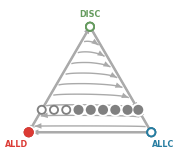

```mathematica
M = 1;
q = 1;
d = SC;
reputationDynamics = Table[ρ[j,M,q]==r[[j]],{j,1,n+1}];
replicatorDynamics = FullSimplify[ df[Range[n]]];
J=FullSimplify[D[replicatorDynamics,{f[[Range[n]]]}]];
equilibria =Quiet@ Solve[replicatorDynamics==ConstantArray[0.0,n],f[[;;n]]];
equilibria = equilibria[[{1,5,4,2,6,3}]];
repEq = First@Quiet[Solve[reputationDynamics/.params,r]];
freqEq = Chop@Quiet@SolveValues[Evaluate[replicatorDynamics/.repEq/.params]==ConstantArray[0.0,n],f[[Range[n]]]];
freeEq = Thread[{fx,fy}->#]&/@Table[freqEq[[1]],{fx,0,freqEq[[1,2,1]],0.1}];
AppendTo[freeEq,Thread[{fx,fy}->(freqEq[[1]]/.fx->freqEq[[1,2,1]])]];
freqEq = Join[Thread[{fx,fy}->#]&/@freqEq[[2;;]],freeEq];
vals=Flatten[Table[
rep = Quiet[Solve[reputationDynamics/.eq/.params,r]];
N@Table[f[[Range[n]]]/.eq/.rr/.params,{rr,Thread[r->#]&/@Feasible[r/.rep]}]
,{eq,freqEq}],1];
freqEq = DeleteDuplicates[Thread[{fx,fy}->#]&/@Feasible[vals]];
stability = Table[
rep = First@Quiet@Solve[Flatten[{Evaluate[reputationDynamics/.eq/.params],0<=r<=1}],r,Reals];
Quiet@Reduce[Re@Eigenvalues[Evaluate[J/.eq/.rep/.params]]<0]
,{eq,freqEq}];
stable = Extract[freqEq,Position[stability,True]];
unstable = Complement[freqEq,stable];
vertex = ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->(Directive[#,PointSize[0.04]]&/@{cx,cy,c11})];
uEq1 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[Gray,PointSize[0.04]],PlotRange->{0,1}];
uEq2 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[White,PointSize[0.025]]];
sEqb =  ListPlot[f[[Range[n]]]/.stable,PlotStyle->Directive[White,PointSize[0.055]],PlotRange->{0,1}];
sEq =  ListPlot[f[[Range[n]]]/.stable,PlotStyle->Directive[Gray,PointSize[0.04]],PlotRange->{0,1}];
pts = Join[Table[{0,x},{x,0.05,0.95,0.05}],Table[{x,0},{x,0.05,0.95,0.05}],Table[{x,1-x},{x,0.05,0.95,0.05}],Table[{x,x},{x,0.07,0.47,0.05}]];
simplex = StreamPlot[Evaluate[replicatorDynamics/.repEq/.params],{fx,0,1},{fy,0,1},
RegionFunction->Function[{x,y},x+y<=1],RegionFillingStyle->None, RegionBoundaryStyle->None,
StreamPoints->pts,StreamColorFunction->None,StreamColorFunctionScaling->False,
StreamStyle->Directive[Lighter@Gray,Thick],StreamScale->{Full,2,0.04}];
off = 0.1;
vlabels = {Graphics[Text[Style["ALLD",8,cy,Bold],{-off,-off}]],Graphics[Text[Style["ALLC",8,cx,Bold],{1+off,-off}]],Graphics[Text[Style["DISC",8,c11,Bold],{1/2,Tan[Pi/3]/2+off}]]}; 
smplx = Show[triangle,Graphics[GeometricTransformation[First@Show[simplex,uEq1,sEqb,sEq,vertex,uEq2],trans]],vlabels,ImageSize->Small]
```

```mathematica
Export[path<>"SC-M1.pdf",smplx,"CompressionLevel"->0,Background->None]
```

./figures/1/SC-M1.pdf

#### (2,1)

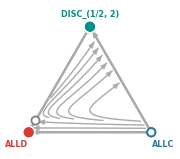

```mathematica
M = 2;
q = 1;
d = SC;
reputationDynamics = Table[ρ[j,M,q]==r[[j]],{j,1,n+1}];
replicatorDynamics = FullSimplify[ df[Range[n]]];
J=FullSimplify[D[replicatorDynamics,{f[[Range[n]]]}]];
equilibria = Quiet@Solve[replicatorDynamics==ConstantArray[0.0,n],f[[;;n]]];
equilibria = equilibria[[{1,5,4,2,6,3}]];
vals=Flatten[Table[
rep = Quiet[Solve[reputationDynamics/.eq/.params,r]];
Table[f[[Range[n]]]/.eq/.rr/.params,{rr,Thread[r->#]&/@Feasible[r/.rep]}]
,{eq,equilibria}],1];
freqEq = DeleteDuplicates[Thread[{fx,fy}->#]&/@Feasible[vals]];
stability = Table[
rep = First@Quiet@Solve[Flatten[{Evaluate[reputationDynamics/.eq/.params],0<=r<=1}],r,Reals];
Reduce[Eigenvalues[Evaluate[J/.eq/.rep/.params]]<0]
,{eq,freqEq}];
repEq =Last[Quiet[Solve[reputationDynamics,r]]];
stable = Extract[freqEq,Position[stability,True]];
unstable = Complement[freqEq,stable];
vertex = ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->(Directive[#,PointSize[0.04]]&/@{cx,cy,c21})];
uEq1 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[Gray,PointSize[0.04]],PlotRange->{0,1}];
uEq2 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[White,PointSize[0.025]]];
sEqb =  ListPlot[f[[Range[n]]]/.stable,PlotStyle->Directive[White,PointSize[0.055]],PlotRange->{0,1}];
pts = Join[Table[{0,x},{x,0.1,0.95,0.85}],Table[{x,0},{x,0.1,0.9,0.8}],Table[{x,1-x},{x,0.1,0.9,0.8}],Table[{x,x},{x,{0.48,0.46,0.4,0.3,0.25,0.2,0.15,0.1}}]];
simplex = StreamPlot[Evaluate[replicatorDynamics/.repEq/.params],{fx,0,1},{fy,0,1},
RegionFunction->Function[{x,y},x+y<=1],RegionFillingStyle->None, RegionBoundaryStyle->None,
StreamPoints->pts(*Thread[{pts,colors}]*),StreamColorFunction->None,StreamColorFunctionScaling->False,
StreamStyle->Directive[Lighter@Gray,Thick],StreamScale->{Full,2,0.04}];
off = 0.1;
vlabels = {Graphics[Text[Style["ALLD",8,cy,Bold],{-off,-off}]],Graphics[Text[Style["ALLC",8,cx,Bold],{1+off,-off}]],Graphics[Text[Style["DISC_(1/2, 2)",8,c21,Bold],{1/2,Tan[Pi/3]/2+off}]]}; 
smplx = Show[triangle,Graphics[GeometricTransformation[First@Show[simplex,uEq1,sEqb,vertex,uEq2],trans]],vlabels,ImageSize->Small]
```

```mathematica
Export[path<>"SC-M2-Q1.pdf",smplx,"CompressionLevel"->0,Background->None]
```

./figures/1/SC-M2-Q1.pdf

#### (2,2)

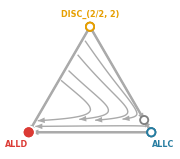

```mathematica
M = 2;
q = 2;
d = SC;
reputationDynamics = Table[ρ[j,M,q]==r[[j]],{j,1,n+1}];
replicatorDynamics = FullSimplify[ df[Range[n]]];
J=FullSimplify[D[replicatorDynamics,{f[[Range[n]]]}]];
equilibria = Quiet@Solve[replicatorDynamics==ConstantArray[0.0,n],f[[;;n]]];
equilibria = equilibria[[{1,5,4,2,6,3}]];
vals=Flatten[Table[
rep = Quiet[Solve[reputationDynamics/.eq/.params,r]];
Table[f[[Range[n]]]/.eq/.rr/.params,{rr,Thread[r->#]&/@Feasible[r/.rep]}]
,{eq,equilibria}],1];
freqEq = DeleteDuplicates[Thread[{fx,fy}->#]&/@Feasible[vals]];
stability = Table[
rep = First@Quiet@Solve[Flatten[{Evaluate[reputationDynamics/.eq/.params],0<=r<=1}],r,Reals];
Reduce[Eigenvalues[Evaluate[J/.eq/.rep/.params]]<0]
,{eq,freqEq}];
repEq =First[Quiet[Solve[reputationDynamics,r]]];
stable = Extract[freqEq,Position[stability,True]];
unstable = Complement[freqEq,stable];
vertex = ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->(Directive[#,PointSize[0.04]]&/@{cx,cy,c22})];
uEq1 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[Gray,PointSize[0.04]],PlotRange->{0,1}];
uEq2 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[White,PointSize[0.025]]];
pts = Join[Table[{0,x},{x,0.1,0.9,0.8}],Table[{x,0},{x,0.1,0.95,0.85}],Table[{x,1-x},{x,0.1,0.9,0.8}],Table[{x,x},{x,{0.47,0.4,0.3,0.2,0.1}}]];
simplex = StreamPlot[Evaluate[replicatorDynamics/.repEq/.params],{fx,0,1},{fy,0,1},
RegionFunction->Function[{x,y},x+y<=1],RegionFillingStyle->None, RegionBoundaryStyle->None,
StreamPoints->pts,StreamColorFunction->None,StreamColorFunctionScaling->False,
StreamStyle->Directive[Lighter@Gray,Thick],StreamScale->{Full,2,0.04}];
sEqb =  ListPlot[f[[Range[n]]]/.stable,PlotStyle->Directive[White,PointSize[0.055]],PlotRange->{0,1}];
off = 0.1;
vlabels = {Graphics[Text[Style["ALLD",8,cy,Bold],{-off,-off}]],Graphics[Text[Style["ALLC",8,cx,Bold],{1+off,-off}]],Graphics[Text[Style["DISC_(2/2, 2)",8,c22,Bold],{1/2,Tan[Pi/3]/2+off}]]}; 
smplx = Show[triangle,Graphics[GeometricTransformation[First@Show[simplex,uEq1,sEqb,vertex,uEq2],trans]],vlabels,ImageSize->Small]
```

```mathematica
Export[path<>"SC-M2-Q2.pdf",smplx,"CompressionLevel"->0,Background->None]
```

./figures/1/SC-M2-Q2.pdf

### Stern-Judging

#### (1,1)

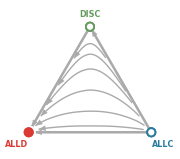

```mathematica
M = 1;
q = 1;
d = SJ;
reputationDynamics = Table[ρ[j,M,q]==r[[j]],{j,1,n+1}];
replicatorDynamics = FullSimplify[ df[Range[n]]];
J=FullSimplify[D[replicatorDynamics,{f[[Range[n]]]}]];
equilibria =Quiet@ Solve[replicatorDynamics==ConstantArray[0.0,n],f[[;;n]]];
equilibria = equilibria[[{1,5,4,2,6,3}]];
vals=Flatten[Table[
rep = Quiet[Solve[reputationDynamics/.eq/.params,r]];
Table[f[[Range[n]]]/.eq/.rr/.params,{rr,Thread[r->#]&/@Feasible[r/.rep]}]
,{eq,equilibria}],1];
freqEq = DeleteDuplicates[Thread[{fx,fy}->#]&/@Feasible[vals]];
stability = Table[
rep = First@Quiet@Solve[Flatten[{Evaluate[reputationDynamics/.eq/.params],0<=r<=1}],r,Reals];
Reduce[Eigenvalues[Evaluate[J/.eq/.rep/.params]]<0]
,{eq,freqEq}];
stable = Extract[freqEq,Position[stability,True]];
unstable = Complement[freqEq,stable];
vertex = ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->(Directive[#,PointSize[0.04]]&/@{cx,cy,c11})];
uEq1 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[Gray,PointSize[0.04]],PlotRange->{0,1}];
uEq2 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[White,PointSize[0.025]]];
pts = Join[Table[{0,x},{x,0.05,0.95,0.05}],Table[{x,0},{x,0.05,0.95,0.05}],Table[{x,1-x},{x,0.05,0.95,0.1}],Table[{x,x},{x,{0.47,0.4,0.3,0.2,0.13,0.08}}]];
simplex = ListStreamPlot[Thread@{pts,GetFlow[reputationDynamics,#[[1]],#[[2]],params]&/@pts},RegionFunction->Function[{x,y},x+y<=1],RegionFillingStyle->None, RegionBoundaryStyle->None,
StreamPoints->pts,StreamColorFunction->None,StreamColorFunctionScaling->False,
StreamStyle->Directive[Lighter@Gray,Thick],StreamScale->{Full,2,0.04}];
sEqb =  ListPlot[f[[Range[n]]]/.stable,PlotStyle->Directive[White,PointSize[0.055]],PlotRange->{0,1}];
off = 0.1;
vlabels = {Graphics[Text[Style["ALLD",8,cy,Bold],{-off,-off}]],Graphics[Text[Style["ALLC",8,cx,Bold],{1+off,-off}]],Graphics[Text[Style["DISC",8,c11,Bold],{1/2,Tan[Pi/3]/2+off}]]}; 
smplx = Show[triangle,Graphics[GeometricTransformation[First@Show[simplex,uEq1,sEqb,vertex,uEq2],trans]],vlabels,ImageSize->Small]
```

```mathematica
Export[path<>"SJ-M1.pdf",smplx,"CompressionLevel"->0,Background->None]
```

./figures/1/SJ-M1.pdf

#### (2,1)

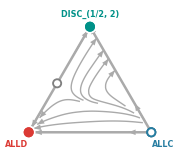

```mathematica
M = 2;
q = 1;
d = SJ;
reputationDynamics = Table[ρ[j,M,q]==r[[j]],{j,1,n+1}];
replicatorDynamics = FullSimplify[ df[Range[n]]];
J=FullSimplify[D[replicatorDynamics,{f[[Range[n]]]}]];
equilibria = Quiet@Solve[replicatorDynamics==ConstantArray[0.0,n],f[[;;n]]];
equilibria = equilibria[[{1,5,4,2,6,3}]];
vals=Flatten[Table[
rep = Quiet[Solve[reputationDynamics/.eq/.params,r]];
Table[f[[Range[n]]]/.eq/.rr/.params,{rr,Thread[r->#]&/@Feasible[r/.rep]}]
,{eq,equilibria}],1];
freqEq = DeleteDuplicates[Thread[{fx,fy}->#]&/@Feasible[vals]];
stability = Table[
rep = First@Quiet@Solve[Flatten[{Evaluate[reputationDynamics/.eq/.params],0<=r<=1}],r,Reals];
Reduce[Eigenvalues[Evaluate[J/.eq/.rep/.params]]<0]
,{eq,freqEq}];
stable = Extract[freqEq,Position[stability,True]];
unstable = Complement[freqEq,stable];
vertex = ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->(Directive[#,PointSize[0.04]]&/@{cx,cy,c21})];
uEq1 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[Gray,PointSize[0.04]],PlotRange->{0,1}];
uEq2 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[White,PointSize[0.025]]];
pts = Join[Table[{0,x},{x,0.1,0.9,0.8}],Table[{x,0},{x,0.05,0.9,0.85}],Table[{x,1-x},{x,0.05,0.9,0.85}],Table[{x,x},{x,{0.45,0.4,0.28,0.2,0.1}}],{{0.4,0.05},{0.06,0.7}}];
simplex = ListStreamPlot[Thread@{pts,GetFlow[reputationDynamics,#[[1]],#[[2]],params]&/@pts},RegionFunction->Function[{x,y},x+y<=1],RegionFillingStyle->None, RegionBoundaryStyle->None,
StreamPoints->pts,StreamColorFunction->None,StreamColorFunctionScaling->False,
StreamStyle->Directive[Lighter@Gray,Thick],StreamScale->{Full,2,0.04}];
sEqb =  ListPlot[f[[Range[n]]]/.stable,PlotStyle->Directive[White,PointSize[0.055]],PlotRange->{0,1}];
off = 0.1;
vlabels = {Graphics[Text[Style["ALLD",8,cy,Bold],{-off,-off}]],Graphics[Text[Style["ALLC",8,cx,Bold],{1+off,-off}]],Graphics[Text[Style["DISC_(1/2, 2)",8,c21,Bold],{1/2,Tan[Pi/3]/2+off}]]}; 
smplx = Show[triangle,Graphics[GeometricTransformation[First@Show[simplex,uEq1,sEqb,vertex,uEq2],trans]],vlabels,ImageSize->Small]
```

```mathematica
Export[path<>"SJ-M2-Q1.pdf",smplx,"CompressionLevel"->0,Background->None]
```

./figures/1/SJ-M2-Q1.pdf

#### (2,2)

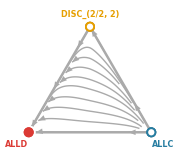

```mathematica
M = 2;
q = 2;
d = SJ;
reputationDynamics = Table[ρ[j,M,q]==r[[j]],{j,1,n+1}];
replicatorDynamics = FullSimplify[ df[Range[n]]];
J=FullSimplify[D[replicatorDynamics,{f[[Range[n]]]}]];
equilibria = Quiet@Solve[replicatorDynamics==ConstantArray[0.0,n],f[[;;n]]];
equilibria = equilibria[[{1,5,4,2,6,3}]];
vals=Flatten[Table[
rep = Quiet[Solve[reputationDynamics/.eq/.params,r]];
Table[f[[Range[n]]]/.eq/.rr/.params,{rr,Thread[r->#]&/@Feasible[r/.rep]}]
,{eq,equilibria}],1];
freqEq = DeleteDuplicates[Thread[{fx,fy}->#]&/@Feasible[vals]];
stability = Table[
rep = First@Quiet@Solve[Flatten[{Evaluate[reputationDynamics/.eq/.params],0<=r<=1}],r,Reals];
Reduce[Eigenvalues[Evaluate[J/.eq/.rep/.params]]<0]
,{eq,freqEq}];
stable = Extract[freqEq,Position[stability,True]];
unstable = Complement[freqEq,stable];
vertex = ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->(Directive[#,PointSize[0.04]]&/@{cx,cy,c22})];
uEq1 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[Gray,PointSize[0.04]],PlotRange->{0,1}];
uEq2 = ListPlot[f[[Range[n]]]/.unstable,PlotStyle->Directive[White,PointSize[0.025]]];
pts = Join[Table[{0,x},{x,0.1,0.9,0.8}],Table[{x,0},{x,0.05,0.9,0.85}],Table[{x,1-x},{x,0.05,0.9,0.85}],Table[{x,x},{x,{0.45,0.4,0.28,0.2,0.1}}],{{0.4,0.05},{0.06,0.7}}];
pts = Join[Table[{0,x},{x,0.1,0.95,0.85}],Table[{x,0},{x,0.1,0.9,0.8}],Table[{x,1-x},{x,0.1,0.9,0.8}],Table[{x,x},{x,0.1,0.45,0.05}]];
simplex = ListStreamPlot[Thread@{pts,GetFlow[reputationDynamics,#[[1]],#[[2]],params]&/@pts},RegionFunction->Function[{x,y},x+y<=1],RegionFillingStyle->None, RegionBoundaryStyle->None,
StreamPoints->pts,StreamColorFunction->None,StreamColorFunctionScaling->False,
StreamStyle->Directive[Lighter@Gray,Thick],StreamScale->{Full,2,0.04}];
sEqb =  ListPlot[f[[Range[n]]]/.stable,PlotStyle->Directive[White,PointSize[0.055]],PlotRange->{0,1}];
off = 0.1;
vlabels = {Graphics[Text[Style["ALLD",8,cy,Bold],{-off,-off}]],Graphics[Text[Style["ALLC",8,cx,Bold],{1+off,-off}]],Graphics[Text[Style["DISC_(2/2, 2)",8,c22,Bold],{1/2,Tan[Pi/3]/2+off}]]}; 
smplx = Show[triangle,Graphics[GeometricTransformation[First@Show[simplex,uEq1,sEqb,vertex,uEq2],trans]],vlabels,ImageSize->Small]
```

```mathematica
Export[path<>"SJ-M2-Q2.pdf",smplx,"CompressionLevel"->0,Background->None]
```

./figures/1/SJ-M2-Q2.pdf

## ED-1

```mathematica
path = "./figures/ED/1/";
```

### Data

```mathematica
(*Trajectories*)
baselineT = Table[
	Chop[Import["../results/trajectories/baseline/"<>n<>"/"<>f<>".csv"],10^-5],
	{n,norms},{f,ToString/@Range[Length[freqs]]}];

unconditionalT = Table[
	Chop[Import["../results/trajectories/unconditional/"<>n<>"/M2/"<>q<>"/"<>f<>".csv"],10^-5],
	{n,norms},{q,Qs},{f,ToString/@Range[Length[freqs]]}];
```

```mathematica
(*Endpoints and cooperation by strategy*)
baselineSS = Table[Chop[ Import["../results/endpoints/interaction/"<>n<>"/baseline/ss-f.csv"],10^-5],
	{n,norms}];
baselineC = Table[Total/@Chop[ Import["../results/endpoints/interaction/"<>n<>"/baseline/coop-f.csv"],10^-5],
	{n,norms}];

unconditionalSS = Table[Chop[ Import["../results/endpoints/interaction/"<>n<>"/unconditional/M2/"<>q<>"/ss-f.csv"],10^-5],
	{n,norms},{q,Qs}];
unconditionalC = Table[Chop[ Import["../results/endpoints/interaction/"<>n<>"/unconditional/M2/"<>q<>"/coop-f.csv"],10^-5],
	{n,norms},{q,Qs}];
```

### Simplexes

```mathematica
Table[Export[path<>norms[[n]]<>"-M1.pdf",
NplotSimplex[baselineT,n,freqs,{cx,cy,c11},{"ALLC","ALLD","DISC"}]
],{n,Length[norms]}]

Table[Export[path<>norms[[n]]<>"-M2-Q"<>ToString[q]<>".pdf",
NplotSimplex[unconditionalT[[n]],q,freqs,{cx,cy,{c21,c22}[[q]]},{"ALLC","ALLD",{"DISC_(1/2, 2)","DISC_(2/2, 2)"}[[q-1]]}]
],{n,Length[norms]},{q,2}]
```

{./figures/ED/1/SC-M1.pdf,./figures/ED/1/SJ-M1.pdf,./figures/ED/1/SS-M1.pdf,./figures/ED/1/SH-M1.pdf}

{{./figures/ED/1/SC-M2-Q1.pdf,./figures/ED/1/SC-M2-Q2.pdf},{./figures/ED/1/SJ-M2-Q1.pdf,./figures/ED/1/SJ-M2-Q2.pdf},{./figures/ED/1/SS-M2-Q1.pdf,./figures/ED/1/SS-M2-Q2.pdf},{./figures/ED/1/SH-M2-Q1.pdf,./figures/ED/1/SH-M2-Q2.pdf}}

### Basins of attraction

```mathematica
Table[
Export[path<>norms[[n]]<>"-M1-bsn.pdf",
inx = OrderingBy[baselineSS[[n]],{-#[[2]],#[[1]],#[[-1]]}&];
Show[Table[getBar[baselineSS[[n]][[inx[[i]]]],{cx,cy,c11},i],{i,1,Length@inx}]],
"CompressionLevel"->0,Background->None
],
{n,Length[norms]}]

Table[
Export[path<>norms[[n]]<>"-M2-Q"<>ToString[q]<>"-bsn.pdf",
inx = OrderingBy[unconditionalSS[[n,q]],{-#[[2]],#[[1]],#[[-1]]}&];
Show[Table[getBar[unconditionalSS[[n,q]][[inx[[i]]]],{cx,cy,{c21,c22}[[q]]},i],{i,1,Length@inx}]],
"CompressionLevel"->0,Background->None
],
{n,Length[norms]},{q,2}]
```

{./figures/ED/1/SC-M1-bsn.pdf,./figures/ED/1/SJ-M1-bsn.pdf,./figures/ED/1/SS-M1-bsn.pdf,./figures/ED/1/SH-M1-bsn.pdf}

{{./figures/ED/1/SC-M2-Q1-bsn.pdf,./figures/ED/1/SC-M2-Q2-bsn.pdf},{./figures/ED/1/SJ-M2-Q1-bsn.pdf,./figures/ED/1/SJ-M2-Q2-bsn.pdf},{./figures/ED/1/SS-M2-Q1-bsn.pdf,./figures/ED/1/SS-M2-Q2-bsn.pdf},{./figures/ED/1/SH-M2-Q1-bsn.pdf,./figures/ED/1/SH-M2-Q2-bsn.pdf}}

## 2

```mathematica
path = "./figures/2/";
```

### Data

```mathematica
(*Trajectories*)
assignmentT = Table[
	Chop[Import["../results/trajectories/assignment/"<>n<>"/Qs/"<>face<>"/"<>f<>".csv"],10^-5],
	{n,norms},{face,ToString/@Range[4]},{f,ToString/@Range[Length[freqs]]}];
```

```mathematica
(*Endpoints and cooperation by strategy*)
assignmentSS = Table[Chop[ Import["../results/endpoints/assignment/"<>n<>"/2/ss-f.csv"],10^-5],
	{n,norms}];
assignmentC = Table[Chop[ Import["../results/endpoints/assignment/"<>n<>"/2/coop-f.csv"],10^-5],
	{n,norms}];
```

### Legend

```mathematica
legend = PointLegend[{cx,cy,c21,c22},(Style[#,20]&/@{
"ALLC",
"ALLD",
"DISC_(1/2)",
"DISC_(2/2)"
}),
LegendMarkerSize->50,LegendLabel->Style["strategy\n",22,Bold],LegendFunction->"Panel"];
Export["./figures/legend.pdf",legend,
"CompressionLevel"->0,Background->None]
```

./figures/legend.pdf

### Simplexes

```mathematica
cq ={{c22,c21,cx},{c21,c22,cy},{cy,cx,c21},{cx,cy,c22}};
```

```mathematica
Table[Export[path<>norms[[n]]<>"/"<>ToString@face<>".pdf",
NplotSimplex[assignmentT[[n]],face,freqs,cq[[face]],{"","",""}]
,"CompressionLevel"->0,Background->None],{n,4},{face,4}]
```

{{./figures/2/SC/1.pdf,./figures/2/SC/2.pdf,./figures/2/SC/3.pdf,./figures/2/SC/4.pdf},{./figures/2/SJ/1.pdf,./figures/2/SJ/2.pdf,./figures/2/SJ/3.pdf,./figures/2/SJ/4.pdf},{./figures/2/SS/1.pdf,./figures/2/SS/2.pdf,./figures/2/SS/3.pdf,./figures/2/SS/4.pdf},{./figures/2/SH/1.pdf,./figures/2/SH/2.pdf,./figures/2/SH/3.pdf,./figures/2/SH/4.pdf}}

### Basins

```mathematica
Table[
Export[path<>norms[[n]]<>"/M2.pdf",
inx = OrderingBy[assignmentSS[[n]],{#[[-1]],-#[[-3]]}&];	
Show[Table[getHBar[assignmentSS[[n]][[inx[[i]]]][[{1,2,4,3}]],{cx,c21,cy,c22},i],{i,1,Length@inx}],AspectRatio->5],
"CompressionLevel"->0,Background->None
],
{n,4}]
```

{./figures/2/SC/M2.pdf,./figures/2/SJ/M2.pdf,./figures/2/SS/M2.pdf,./figures/2/SH/M2.pdf}

## ED2

```mathematica
path = "./figures/ED/2/";
```

### Basins

```mathematica
Table[
Export[path<>norms[[n]]<>"-Q"<>ToString[q]<>".pdf",
inx = OrderingBy[unconditionalSS[[n,q]],{#[[2]],#[[1]],#[[-1]]}&];
Show[Table[getHBar[unconditionalSS[[n,q]][[inx[[i]]]][[{2,1,3}]],{cy,cx,{c21,c22}[[q]]},i],{i,1,Length@inx}],AspectRatio->5],
"CompressionLevel"->0,Background->None
],
{n,4},{q,2}]

Table[
Export[path<>norms[[n]]<>"-M2.pdf",
inx = OrderingBy[assignmentSS[[n]],{#[[-1]],-#[[-3]]}&];	
Show[Table[getHBar[assignmentSS[[n]][[inx[[i]]]][[{1,2,4,3}]],{cx,c21,cy,c22},i],{i,1,Length@inx}],AspectRatio->5],
"CompressionLevel"->0,Background->None
],
{n,Length@norms}]
```

{{./figures/ED/2/SC-Q1.pdf,./figures/ED/2/SC-Q2.pdf},{./figures/ED/2/SJ-Q1.pdf,./figures/ED/2/SJ-Q2.pdf},{./figures/ED/2/SS-Q1.pdf,./figures/ED/2/SS-Q2.pdf},{./figures/ED/2/SH-Q1.pdf,./figures/ED/2/SH-Q2.pdf}}

{./figures/ED/2/SC-M2.pdf,./figures/ED/2/SJ-M2.pdf,./figures/ED/2/SS-M2.pdf,./figures/ED/2/SH-M2.pdf}

## 3ab & ED-3,4

### Data

```mathematica
sweep = Table[
Import["../results/endpoints/robustness/q/"<>n<>"/"<>b<>"-"<>ϵ<>"/"<>M<>"/ss-f.csv"],
{n,norms[[1;;2]]},{M,ToString/@Range[2,6]},{ϵ,ToString/@eps},{b,bs}];
```

### 3a

```mathematica
path = "./figures/3/";
```

```mathematica
Table[Export[path<>norms[[n]]<>"-a.pdf",
GraphicsRow@Table[
inx = OrderingBy[sweep[[n,m,2,-2]],{#[[1]],#[[2]],#[[-1]]}&];
c = Table[Blend[cs,i/(1+m)],{i,1+m}];
colors = Flatten@{cx,cy,c};
Show[Graphics[{
Table[
data = sweep[[n,m,2,-2]][[inx[[x]]]];
Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{If[i==1,0,h*Total[data[[1;;i-1]]]],(x*width)},
			{h*Total[data[[1;;i]]],(x*width)+width}
			]
			},
		{i,1,Length[data]}],
{x,1,Length@inx}]
,
data = sweep[[n,m,2,-2]][[inx]];
present = Sign[data];
sets = DeleteDuplicates[present];
inxSS = Position[present,#]&/@sets;
discs = Extract[sets,Position[sets,{0,0,__}]];
nms = If[Length[discs]>0,
strats = Internal`RationalNoReduce[#,(1+m)]&/@(Flatten[Position[Extract[discs,Ordering[Count[present,#]&/@discs,-1]],1]]-2);
Riffle[ToString[#,TraditionalForm]&/@strats,","],
""];
Inset[Style[Text[StringJoin[nms]],18,White,Bold],{Center,1}]},AspectRatio->3],
ImageSize->Small],
{m,5}],
"CompressionLevel"->0,Background->None],
{n,2}]
```

{./figures/3/SC-a.pdf,./figures/3/SJ-a.pdf}

### 3b

```mathematica
M = 6;
c = Table[Blend[cs,i/M],{i,M}];
fnz = Table[Sum[Binomial[M,m] p^m (1-p)^(M-m),{m,Ceiling[q],M}],{q,M}];
pm = Plot[{fnz},{p,0,1},
PlotRange->{0.,1.02},
PlotStyle->(Directive[#,Thick]&/@Flatten[{c}]),
Frame->True,FrameTicks->{{Range[0.2,1.0,0.2],None},{{0,1},None}},
FrameTicksStyle->7,
FrameLabel->{{Style["probability aggregated\nreputation is good",7,FontFamily->"Arial"],None},{Style["probability random observation is good",7,FontFamily->"Arial"],None}},
ImageSize->Small];
Export[path<>"Q-reps.pdf",pm,
"CompressionLevel"->0,Background->None]
```

./figures/3/Q-reps.pdf

### ED-3,4

```mathematica
path = "./figures/ED/3-4/";
```

```mathematica
Table[
Export[path<>norms[[n]]<>"-M"<>ToString[m]<>".pdf",
Show[GraphicsGrid@Table[
inx = OrderingBy[sweep[[n,m,e,b]],{#[[1]],#[[2]],#[[-1]]}&];
c = Table[Blend[cs,i/(1+m)],{i,1+m}];
colors = Flatten@{cx,cy,c};
Graphics[{
Table[
data = sweep[[n,m,e,b]][[inx[[x]]]];
Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{If[i==1,0,h*Total[data[[1;;i-1]]]],(x*width)},
			{h*Total[data[[1;;i]]],(x*width)+width}
			]
			},
		{i,1,Length[data]}],
{x,1,Length@inx}]
,
data = sweep[[n,m,e,b]][[inx]];
present = Sign[data];
sets = DeleteDuplicates[present];
inxSS = Position[present,#]&/@sets;
discs = Extract[sets,Position[sets,{0,0,__}]];
nms = If[Length[discs]>0,
strats = Internal`RationalNoReduce[#,(1+m)]&/@(Flatten[Position[Extract[discs,Ordering[Count[present,#]&/@discs,-1]],1]]-2);
Riffle[ToString[#,TraditionalForm]&/@strats,","],
""];
Inset[Style[Text[StringJoin[nms]],12.5,White,Bold],{Center,2}]},AspectRatio->3],
{e,Length[eps],1,-1},{b,Length[bs]}],ImageSize->110],
"CompressionLevel"->0,Background->None]
,{m,1,5},{n,1,2}]
```

{{./figures/ED/3-4/SC-M1.pdf,./figures/ED/3-4/SJ-M1.pdf},{./figures/ED/3-4/SC-M2.pdf,./figures/ED/3-4/SJ-M2.pdf},{./figures/ED/3-4/SC-M3.pdf,./figures/ED/3-4/SJ-M3.pdf},{./figures/ED/3-4/SC-M4.pdf,./figures/ED/3-4/SJ-M4.pdf},{./figures/ED/3-4/SC-M5.pdf,./figures/ED/3-4/SJ-M5.pdf}}

```mathematica
legend = BarLegend[{cs,{0,1}},9,LabelStyle->16,LegendFunction->"Panel",LegendLabel->Style["q",16,Bold]];
Export[path<>"legend.pdf",legend,
"CompressionLevel"->0,Background->None]
legs = PointLegend[{cx,cy},(Style[#,16]&/@{
"ALLC",
"ALLD"}),
LegendMarkerSize->35,LegendLabel->Style["unconditional\n   strategies\n",16, Bold],LegendFunction->"Panel"];
Export[path<>"legendUS.pdf",legs,
"CompressionLevel"->0,Background->None]
```

./figures/ED/3-4/legend.pdf

./figures/ED/3-4/legendUS.pdf

## 3cd & ED-6,7

### Params

```mathematica
qs = {1/5,1/4,1/3,2/5,1/2,3/5,2/3,3/4,4/5,1.0}[[{2,3,5,7,8,10}]];
ms = {{5,10},{4,8},{3,6,9},{5,10},{2,4,6,8,10},{5,10},{3,6,9},{4,8},{5,10},{1,2,3,4,5,6,7,8,9,10}}[[{2,3,5,7,8,10}]];
```

### Data

```mathematica
sweepO = Table[
Import["../results/endpoints/robustness/M/"<>n<>"/"<>b<>"-"<>ϵ<>"/"<>q<>"/ss-f.csv"],
{n,norms[[1;;2]]},{q,ToString/@{2,3,5,7,8,10}},{ϵ,ToString/@eps},{b,bs}];
```

### 3c

```mathematica
path = "./figures/3/";
```

```mathematica
Table[Export[path<>norms[[n]]<>"-c.pdf",
GraphicsRow@Table[
inx = OrderingBy[sweepO[[n,q,2,-2]],{#[[2]],#[[1]],#[[-1]]}&];
c = Extract[csM,Position[ms[[1;;4]]//Flatten//DeleteDuplicates//Sort,#]&/@ms[[q]]];
colors = Flatten@{cx,cy,c};
Show[Graphics[{
Table[
data = sweepO[[n,q,2,-2]][[inx[[x]]]];
Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{If[i==1,0,h*Total[data[[1;;i-1]]]],(x*width)},
			{h*Total[data[[1;;i]]],(x*width)+width}
			]
			},
		{i,1,Length[data]}],
{x,1,Length@inx}]
},AspectRatio->3],
ImageSize->Small],
{q,4}],
"CompressionLevel"->0,Background->None],
{n,2}]
```

{./figures/3/SC-c.pdf,./figures/3/SJ-c.pdf}

#### Legends for columns

```mathematica
Table[Export[path<>"leg-"<>ToString[q]<>".pdf",
SwatchLegend[
Flatten@Extract[csM,Position[ms[[1;;4]]//Flatten//DeleteDuplicates//Sort,#]&/@ms[[q]]],
ms[[q]],
LegendLayout->"Column",LegendMarkerSize->12,LabelStyle->10
],
"CompressionLevel"->0,Background->None],
{q,1,4}]
```

{./figures/3/leg-1.pdf,./figures/3/leg-2.pdf,./figures/3/leg-3.pdf,./figures/3/leg-4.pdf}

### 3d

```mathematica
res = Table[Import["../results/reputations/"<>norms[[n]]<>"/"<>ToString@m<>".csv"],{n,2},{m,{2,4,6,8,10}}];
```

```mathematica
c = Flatten@Extract[csM,Position[ms[[1;;4]]//Flatten//DeleteDuplicates//Sort,#]&/@ms[[3]]];
```

```mathematica
Table[
plt=Table[
ListLinePlot[Thread[{Ms,#}]&/@res[[n,{1,2,-1}[[i]],2;;3]],
PlotStyle->{Directive[Dashed,Thickness[0.0075],c[[{1,2,-1}[[i]]]]],Directive[Thickness[0.0075],c[[{1,2,-1}[[i]]]]]},
Frame->True,PlotRange->{0.988,1.001},
FrameTicks->{{{0.988,0.995,1.},None},Automatic},
FrameTicksStyle->7,
FrameLabel->{{Style["reputation",7,FontFamily->"Arial"],None},{Style["number of observations of invader (M_I)",7,FontFamily->"Arial"],None}},
ImageSize->Small
],{i,3}]//Show;
plt = Show[plt,
Show[Table[
ListPlot[{{Ms[[{1,2,-1}[[i]]]],res[[n,{1,2,-1}[[i]],3]][[{1,2,-1}[[i]]]]}},
PlotMarkers->{Automatic,10},PlotStyle->Black],{i,3}]],
Show[Table[
ListPlot[{{Ms[[{1,2,-1}[[i]]]],res[[n,{1,2,-1}[[i]],3]][[{1,2,-1}[[i]]]]}},
PlotMarkers->{Automatic,8},PlotStyle->c[[{1,2,-1}[[i]]]]],{i,3}]]
];
Export[path<>norms[[n]]<>"-reps.pdf",plt,
"CompressionLevel"->0,Background->None],
{n,2}]
```

{./figures/3/SC-reps.pdf,./figures/3/SJ-reps.pdf}

```mathematica
legend = PointLegend[c[[{1,2,-1}]],(Style[#,20]&/@{
"2",
"4",
"10"
}),
LegendMarkerSize->45,LegendLabel->Style["   number of \nobservations\nof resident (M_R)",22,FontFamily->"Arial"],LegendFunction->"Panel",LegendLayout->"Row"];
Export[path<>"leg1-reps.pdf",legend,
"CompressionLevel"->0,Background->None]
legend = LineLegend[{Directive[Gray,Thickness[0.025]],Directive[Gray,Thickness[0.025],Dashed]},(Style[#,20,FontFamily->"Arial"]&/@{
"residents's view of invader",
"invader's view of resident"
}),
LegendMarkerSize->45,LegendLabel->Style["reputations",22,FontFamily->"Arial"],LegendFunction->"Panel"];
Export[path<>"leg2-reps.pdf",legend,
"CompressionLevel"->0,Background->None]
```

./figures/3/leg1-reps.pdf

./figures/3/leg2-reps.pdf

### ED-6,7

```mathematica
path = "./figures/ED/6-7/";
```

```mathematica
Table[Export[path<>norms[[n]]<>"-q"<>ToString[q]<>".pdf",
Show[GraphicsGrid@Table[
inx = OrderingBy[sweepO[[n,q,e,b]],{#[[1]],#[[2]],#[[-1]]}&];
c = Extract[csM,Position[ms[[1;;4]]//Flatten//DeleteDuplicates//Sort,#]&/@ms[[q]]];
colors = Flatten@{cx,cy,c};
Show[Table[getHBar[sweepO[[n,q,e,b]][[inx[[i]]]],
colors,i],
{i,1,Length@inx}],AspectRatio->3],
{e,Length[eps],1,-1},{b,Length[bs]}],
ImageSize->110],
"CompressionLevel"->0,Background->None],
{n,2},{q,5}]
```

{{./figures/ED/6-7/SC-q1.pdf,./figures/ED/6-7/SC-q2.pdf,./figures/ED/6-7/SC-q3.pdf,./figures/ED/6-7/SC-q4.pdf,./figures/ED/6-7/SC-q5.pdf},{./figures/ED/6-7/SJ-q1.pdf,./figures/ED/6-7/SJ-q2.pdf,./figures/ED/6-7/SJ-q3.pdf,./figures/ED/6-7/SJ-q4.pdf,./figures/ED/6-7/SJ-q5.pdf}}

```mathematica
Table[Export[path<>"leg-"<>ToString[q]<>".pdf",
SwatchLegend[
Flatten@Extract[csM,Position[ms[[1;;4]]//Flatten//DeleteDuplicates//Sort,#]&/@ms[[q]]],
ms[[q]],
LegendLayout->"Column",LegendMarkerSize->14,LabelStyle->16,LegendFunction->"Panel",LegendLabel->Style["M",16,Bold]
],
"CompressionLevel"->0,Background->None],
{q,1,5}]
legs = PointLegend[{cx,cy},(Style[#,16]&/@{
"ALLC",
"ALLD"}),
LegendMarkerSize->35,LegendLabel->Style["unconditional\n   strategies\n",16, Bold],LegendFunction->"Panel"];
Export[path<>"legendUS.pdf",legs,
"CompressionLevel"->0,Background->None]
```

{./figures/ED/6-7/leg-1.pdf,./figures/ED/6-7/leg-2.pdf,./figures/ED/6-7/leg-3.pdf,./figures/ED/6-7/leg-4.pdf,./figures/ED/6-7/leg-5.pdf}

./figures/ED/6-7/legendUS.pdf

## ED-5

```mathematica
path = "./figures/ED/5/";
```

### Legend

```mathematica
legend = PointLegend[{cy,c11,c21,c22,Lighter@cx},(Style[#,20]&/@{
"ALLD",
"DISC",
"DISC_(1/2)",
"DISC_(2/2)",
"probC"
}),
LegendMarkerSize->50,LegendLabel->Style["strategy\n",22,Bold],LegendFunction->"Panel"];
Export[path<>"legend.pdf",legend,
"CompressionLevel"->0,Background->None]
```

./figures/ED/5/legend.pdf

### Flow

```mathematica
ps = Range[0.0,1.0,0.1];
pps = Flatten@{"0.0",ToString/@Range[0.1,0.9,0.1],"1.0"};
fqs = Range[0.05,0.95,0.05];
pss =ToString/@Range[0.1,0.9,0.1];
```

```mathematica
pc = Table[Last@Transpose@Import["../results/endpoints/probabilistic-cooperator/"<>n<>"/M"<>{"1","2","2"}[[m]]<>"/PROB-"<>{"DISC","LTFO","LTFN"}[[m]]<>"/"<>ToString[p]<>"/ss-f.csv"],
{n,norms[[1;;1]]},{m,1,3},{p,pps}];
```

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M1/PROB-DISC/0.0/ss-f.csv not found during Import.

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M1/PROB-DISC/0.1/ss-f.csv not found during Import.

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M1/PROB-DISC/0.2/ss-f.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
Table[Export[path<>norms[[n]]<>{"-M1","-M2-Q1","-M2-Q2"}[[m]]<>".pdf",
pts=Table[
{ps[[i]],If[Length@DeleteDuplicates[Sign@pc[[n,m,i]]]>1,
Extract[1-fqs+0.025,FirstPosition[pc[[n,m,i]],Last[DeleteDuplicates[pc[[n,m,i]]]]]],1.0]},{i,Length[ps]}];
Show[
(*Arrows*)
Table[Graphics[{Blend[Flatten@{Lighter@cx,{c11,c21,c22}[[m]]},pc[[n,m,i,j]]],Arrowheads[0.075],Thickness[0.015],Arrow[{{ps[[i]],1-fqs[[j]]},{ps[[i]],pc[[n,m,i,j]]}},0.015]}],{i,Length[ps]},{j,Length[fqs]}],
(*Unstable*)
Graphics[{Black,PointSize[0.025],Point[#]}]&/@pts,
Table[Graphics[{Black,PointSize[0.025],Point[{ps[[i]],0}]}],{i,Length[ps]},{j,Length[fqs]}],
Table[Graphics[{White,PointSize[0.015],Point[{ps[[i]],0}]}],{i,Length[ps]},{j,Length[fqs]}],
Graphics[{White,PointSize[0.015],Point[#]}]&/@pts,
(*Stable*)
Table[Graphics[{Black,PointSize[0.025],Point[{ps[[i]],pc[[n,m,i,j]]}]}],{i,Length[ps]},{j,Length[fqs]}]
,AspectRatio->1],
"CompressionLevel"->0,Background->None],
{n,1},{m,3}]
```

Part::partd: Part specification {{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»}}}⟦1,1,1,1⟧ is longer than depth of object.

Blend::argl: {{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»}}}⟦1,1,1,1⟧ should be a real number or a list of non-negative numbers, which has the same length as {color,color}.

Part::partd: Part specification {{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»}}}⟦1,1,1,1⟧ is longer than depth of object.

Part::partd: Part specification {{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»}}}⟦1,1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Blend::argl: {{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»}}}⟦1,1,1,2⟧ should be a real number or a list of non-negative numbers, which has the same length as {color,color}.

Blend::argl: {{{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»},{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,«1»}}}⟦1,1,1,3⟧ should be a real number or a list of non-negative numbers, which has the same length as {color,color}.

General::stop: Further output of Blend::argl will be suppressed during this calculation.

{{./figures/ED/5/SC-M1.pdf,./figures/ED/5/SC-M2-Q1.pdf,./figures/ED/5/SC-M2-Q2.pdf}}

### Basins

```mathematica
pcU = Table[Import["../results/endpoints/probabilistic-cooperator/"<>n<>"/M1/PROB-ALLD-DISC/"<>ToString[p]<>"/ss-f.csv"],
{n,norms[[1;;1]]},{p,pss}];
Export[path<>norms[[1]]<>"-pC-ALLD-DISC.pdf",
GraphicsRow@Table[
inx = OrderingBy[pcU[[1,j]],{#[[2]],#[[1]],#[[-1]]}&];
Show[Table[getHBar[pcU[[1,j]][[inx[[i]]]][[{2,1,3}]],{cy,Lighter@cx,c11},i],{i,1,Length@inx}],AspectRatio->5]
,{j,Length[pss]}],
"CompressionLevel"->0,Background->None]
```

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M1/PROB-ALLD-DISC/0.1/ss-f.csv not found during Import.

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M1/PROB-ALLD-DISC/0.2/ss-f.csv not found during Import.

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M1/PROB-ALLD-DISC/0.3/ss-f.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

OrderingBy::normal: Nonatomic expression expected at position 1 in OrderingBy[$Failed,{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&].

Part::pkspec1: The expression $Failed cannot be used as a part specification.

Part::partw: Part {2,1,3} of $Failed⟦$Failed⟧ does not exist.

Part::pkspec1: The expression {#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}& cannot be used as a part specification.

Part::partw: Part {2,1,3} of $Failed⟦{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&⟧ does not exist.

OrderingBy::normal: Nonatomic expression expected at position 1 in OrderingBy[$Failed,{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&].

Part::pkspec1: The expression $Failed cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part {2,1,3} of $Failed⟦$Failed⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

OrderingBy::normal: Nonatomic expression expected at position 1 in OrderingBy[$Failed,{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&].

General::stop: Further output of OrderingBy::normal will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}] is not a valid replacement rule.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}],{ImagePadding,ImageSize,AspectRatio}] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{System`Dump`opts}].

General::stop: Further output of Median::rectn will be suppressed during this calculation.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,2⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,2⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

General::stop: Further output of DeleteMissing::invrp will be suppressed during this calculation.

MapThread::mptd: Object Graphics`GraphicsGridDump`sizes$346212 at position {2, 1} in MapThread[Graphics`GraphicsGridDump`DividerCoordinates,{Graphics`GraphicsGridDump`sizes$346212,Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346212]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object -Graphics`GraphicsGridDump`sizes$346212 at position {2, 1} in MapThread[Graphics`GraphicsGridDump`DividerCoordinates,{-Graphics`GraphicsGridDump`sizes$346212,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346212]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object Min[-Graphics`GraphicsGridDump`sizes$346212,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346212]] at position {2, 1} in MapThread[{Graphics`GraphicsGridDump`DividerCoordinates,Graphics`GraphicsGridDump`DividerCoordinates},{Min[-Graphics`GraphicsGridDump`sizes$346212,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346212]],Max[-Graphics`GraphicsGridDump`sizes$346212,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346212]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

./figures/ED/5/SC-pC-ALLD-DISC.pdf

```mathematica
pcU = Table[Import["../results/endpoints/probabilistic-cooperator/"<>n<>"/M2/PROB-ALLD-LTFO-LTFN/"<>ToString[p]<>"/ss-f.csv"],
{n,norms[[1;;1]]},{p,pss}];
Export[path<>norms[[1]]<>"-pC-ALLD-LTFO-LTFN.pdf",
GraphicsRow@Table[
inx = OrderingBy[pcU[[1,j]],{#[[2]],#[[1]],#[[-1]]}&];
Show[Table[getHBar[pcU[[1,j]][[inx[[i]]]][[{2,1,3,4}]],{cy,Lighter@cx,c21,c22},i],{i,1,Length@inx}],AspectRatio->5]
,{j,Length[pss]}],
"CompressionLevel"->0,Background->None]
```

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M2/PROB-ALLD-LTFO-LTFN/0.1/ss-f.csv not found during Import.

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M2/PROB-ALLD-LTFO-LTFN/0.2/ss-f.csv not found during Import.

Import::nffil: File ../results/endpoints/probabilistic-cooperator/SC/M2/PROB-ALLD-LTFO-LTFN/0.3/ss-f.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

OrderingBy::normal: Nonatomic expression expected at position 1 in OrderingBy[$Failed,{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&].

Part::pkspec1: The expression $Failed cannot be used as a part specification.

Part::partw: Part {2,1,3,4} of $Failed⟦$Failed⟧ does not exist.

Part::pkspec1: The expression {#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}& cannot be used as a part specification.

Part::partw: Part {2,1,3,4} of $Failed⟦{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&⟧ does not exist.

OrderingBy::normal: Nonatomic expression expected at position 1 in OrderingBy[$Failed,{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&].

Part::pkspec1: The expression $Failed cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part {2,1,3,4} of $Failed⟦$Failed⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

OrderingBy::normal: Nonatomic expression expected at position 1 in OrderingBy[$Failed,{#1⟦2⟧,#1⟦1⟧,#1⟦-1⟧}&].

General::stop: Further output of OrderingBy::normal will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

FilterRules::rep: FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}] is not a valid replacement rule.

Lookup::invrl: The argument FilterRules[FilterRules[System`Private`SortOptions[$Failed],{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,«28»}],{ImagePadding,ImageSize,AspectRatio}] is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

FilterRules::rep: System`Private`SortOptions[$Failed] is not a valid replacement rule.

General::stop: Further output of FilterRules::rep will be suppressed during this calculation.

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{System`Dump`opts}].

General::stop: Further output of Median::rectn will be suppressed during this calculation.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,2⟧ is longer than depth of object.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,2⟧ is not a valid Association or a list.

Part::partd: Part specification {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DeleteMissing::invrp: The argument {{Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],Lookup[System`Dump`opts,System`Dump`name],{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}}⟦All,All,2,1⟧ is not a valid Association or a list.

General::stop: Further output of DeleteMissing::invrp will be suppressed during this calculation.

MapThread::mptd: Object Graphics`GraphicsGridDump`sizes$346468 at position {2, 1} in MapThread[Graphics`GraphicsGridDump`DividerCoordinates,{Graphics`GraphicsGridDump`sizes$346468,Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346468]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object -Graphics`GraphicsGridDump`sizes$346468 at position {2, 1} in MapThread[Graphics`GraphicsGridDump`DividerCoordinates,{-Graphics`GraphicsGridDump`sizes$346468,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346468]}] has only 0 of required 1 dimensions.

MapThread::mptd: Object Min[-Graphics`GraphicsGridDump`sizes$346468,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346468]] at position {2, 1} in MapThread[{Graphics`GraphicsGridDump`DividerCoordinates,Graphics`GraphicsGridDump`DividerCoordinates},{Min[-Graphics`GraphicsGridDump`sizes$346468,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346468]],Max[-Graphics`GraphicsGridDump`sizes$346468,-Graphics`GraphicsGridDump`ExpandOption[Spacings,Scaled[0.1],{2,10},Graphics`GraphicsGridDump`sizes$346468]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

./figures/ED/5/SC-pC-ALLD-LTFO-LTFN.pdf

## 4 & ED-10

```mathematica
path = "./figures/4/";
```

### Bars

```mathematica
ηs={"0.1","0.5","0.9"};
ws = {"0.1","0.5","0.9","1.0"};
clrs = {cx,cy,c21,c22,Lighter@cx,Lighter@cy,Lighter@c21,Lighter@c22};
Table[
fxn = Table[Import["../results/endpoints/norms/independent/M2/"<>norms[[n1]]<>"-"<>norms[[n2]]<>"/"<>w<>"-"<>η<>"/ss.csv"],{η,ηs}];
bars = GraphicsRow@Table[
inx = OrderingBy[fxn[[n]],{#[[2]]}&];
base=Show[Table[getHBar[fxn[[n]][[inx[[i]]]],clrs,i],{i,1,Length@inx}],AspectRatio->5],{n,Length[ηs]}];
Export[path<>ToString@w<>".pdf",bars,
"CompressionLevel"->0,Background->None]
,{n1,1,1},{n2,n1+1,2},{w,ws}]
```

{{{./figures/4/0.1.pdf,./figures/4/0.5.pdf,./figures/4/0.9.pdf,./figures/4/1.0.pdf}}}

### Network

```mathematica
nodes={"A","B","C","D","E","F","G","H","I","J"};
edges=UndirectedEdge@@@Subsets[nodes,{2}];
pos=AssociationThread[nodes->CirclePoints[Length[nodes]]];
nodeColors={Lighter@cx,cx,Lighter@cy,cy,Lighter@c21,Lighter@c21,c21,c21,Lighter@c22,c22};
graph=Graph[nodes,edges,VertexCoordinates->pos,
VertexStyle->Thread[nodes->(Directive[#,EdgeForm[None]]&/@nodeColors)],VertexShapeFunction->"Circle",
EdgeStyle->Directive[Lighter[Gray,0.7],Thick],VertexSize->Large,ImageSize->Small];
Export[path<>"net.pdf",graph,"CompressionLevel"->0,Background->None]
```

./figures/4/net.pdf

```mathematica
legend = PointLegend[{Gray,LightGray},(Style[#,6.5,FontFamily->"Arial"]&/@{"Scoring","Stern-Judging"}), LegendMarkerSize->20,LegendLabel->Style["social norms",FontFamily->"Arial",7],
LegendFunction->"Panel"]
```

### ED-10

```mathematica
path = "./figures/ED/10/";
```

```mathematica
η = "0.5";
ws = {"0.1","0.5","0.9","1.0"};
clrs = {cx,cy,c21,c22,Lighter@cx,Lighter@cy,Lighter@c21,Lighter@c22};
Table[
bars = GraphicsRow@Table[
fxn = Import["../results/endpoints/norms/independent/M2/"<>norms[[n1]]<>"-"<>norms[[n2]]<>"/"<>w<>"-"<>η<>"/ss.csv"];
inx = OrderingBy[fxn,{#[[2]],#[[6]]}&];
bar=Show[Table[getHBar[fxn[[inx[[i]]]],clrs,i],{i,1,Length@inx}],AspectRatio->5];
bar,{w,ws}];
Export[path<>norms[[n1]]<>"-"<>norms[[n2]]<>".pdf",bars,
"CompressionLevel"->0,Background->None]
,{n1,1,3},{n2,n1+1,4}]
```

{{./figures/ED/10/SC-SJ.pdf,./figures/ED/10/SC-SS.pdf,./figures/ED/10/SC-SH.pdf},{./figures/ED/10/SJ-SS.pdf,./figures/ED/10/SJ-SH.pdf},{./figures/ED/10/SS-SH.pdf}}

```mathematica
legend1 = PointLegend[{cx,cy,c21,c22},
(Style[#,7]&/@{"ALLC","ALLD","DISC_(1/2, 2)","DISC_(2/2, 2)"}),
LegendMarkerSize->25];
legend2 = PointLegend[Lighter/@{cx,cy,c21,c22},
(Style[#,7]&/@{"ALLC","ALLD","DISC_(1/2, 2)","DISC_(2/2, 2)"}),
LegendMarkerSize->25];
Export[path<>"/legend1.pdf",legend1,
"CompressionLevel"->0,Background->None]
Export[path<>"/legend2.pdf",legend2,
"CompressionLevel"->0,Background->None]
```

./figures/ED/10//legend1.pdf

./figures/ED/10//legend2.pdf

## ED-8

```mathematica
path = "./figures/ED/8/";
```

### Data

```mathematica
resmin = Table[Flatten@Import["../results/reputations/"<>norms[[1]]<>"/"<>ToString@m<>"-min.csv"],{m,{2,4,6,8,10}}];
```

### Plot

```mathematica
rp = Show[
ListLogLogPlot[Thread[{Range[0.01,0.1,0.01],#}]&/@resmin,
Joined->True,ImageSize->800,PlotStyle-> Extract[csM,Position[ms[[1;;4]]//Flatten//DeleteDuplicates//Sort,#]&/@ms[[3]]],
Frame->True,FrameTicksStyle->20,FrameLabel->(Style[#,22]&/@{"error rates (ϵ,α)","benefit-to-cost ratio (b/c)"})
],
ListLogLogPlot[Thread[{{0.01,0.02,0.05,0.1},10}],Joined->True,PlotStyle->Directive[Gray,Dashed]],
ListLogLogPlot[{#}&/@Thread[{{0.01,0.02,0.05,0.1},10}],PlotMarkers->{Automatic,17},PlotStyle->Lighter@Gray]
];
Export[path<>"competitionM.pdf", rp,"CompressionLevel"->0,Background->None]
```

./figures/ED/8/competitionM.pdf

```mathematica
Table[Export[path<>norms[[n]]<>"-e"<>ToString[e]<>".pdf",
inx = OrderingBy[sweepO[[n,q,e,b]],{#[[1]],#[[2]],#[[-1]]}&];
c = Extract[csM,Position[ms[[1;;4]]//Flatten//DeleteDuplicates//Sort,#]&/@ms[[q]]];
colors = Flatten@{cx,cy,c};
Show[Table[getHBar[sweepO[[n,q,e,b]][[inx[[i]]]],
colors,i],
{i,1,Length@inx}],AspectRatio->3],
"CompressionLevel"->0,Background->None],
{e,1,4},{b,5,5},{n,1},{q,3,3}]
```

{{{{./figures/ED/8/SC-e1.pdf}}},{{{./figures/ED/8/SC-e2.pdf}}},{{{./figures/ED/8/SC-e3.pdf}}},{{{./figures/ED/8/SC-e4.pdf}}}}

## ED-9

```mathematica
path = "./figures/ED/9/";
```

### Data

```mathematica
n=1;
```

```mathematica
opt = Table[Chop[ Import["../results/endpoints/coevolution/opt/"<>norms[[n]]<>"/"<>ToString[m]<>"/ss-f.csv"],10^-5],
	{m,2,8,2}];
coev = Table[Import["../results/endpoints/coevolution/"<>norms[[n]]<>"/2-"<>ToString[m]<>"/ss-f.csv"],
{m,{4,6,8}}];
```

### Legends

```mathematica
Table[
Export[path<>"leg-"<>ToString[m+1]<>".png",
SwatchLegend[
Table[Blend[cs,i/(1+m)],{i,1+m}],
Table[ Internal`RationalNoReduce[i,(1+m)],{i,1+m}],
LegendLayout->"Column",LegendMarkerSize->14,LabelStyle->16,LegendFunction->"Panel",LegendLabel->Style["q",16,Bold]
],
"CompressionLevel"->0,Background->None]
,{m,{3,5,7}}]
```

{./figures/ED/9/leg-4.png,./figures/ED/9/leg-6.png,./figures/ED/9/leg-8.png}

```mathematica
Table[
Export[path<>"leg-"<>ToString[m+1]<>".png",
SwatchLegend[
{c21,Darker@c21},
Table[ Internal`RationalNoReduce[i,(1+m)],{i,1+m}],
LegendLayout->"Column",LegendMarkerSize->14,LabelStyle->16,LegendFunction->"Panel",LegendLabel->Style["q",16,Bold]
],
"CompressionLevel"->0,Background->None]
,{m,{1}}]
```

{./figures/ED/9/leg-2.png}

### Base

```mathematica
Table[
Export[path<>"opt-"<>ToString[2]<>".pdf",
inx = OrderingBy[opt[[m]],{#[[2]],#[[1]],#[[-1]]}&];
c = {c21,Darker@c21};
colors = Flatten@{cx,cy,c};
Graphics[{
Table[
data = opt[[m]][[inx[[x]]]];
Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{If[i==1,0,0.1*Total[data[[1;;i-1]]]],(x)},
			{0.1*Total[data[[1;;i]]],x+1}
			]
			},
		{i,1,Length[data]}],
{x,1,Length@inx}]
,
data = opt[[m]][[inx]];
present = Sign[data];
sets = DeleteDuplicates[present];
inxSS = Position[present,#]&/@sets;
discs = Extract[sets,Position[sets,{0,0,__}]];
nms = If[Length[discs]>0,
strats = Internal`RationalNoReduce[#,(1+m)]&/@(Flatten[Position[Extract[discs,Ordering[Count[present,#]&/@discs,-1]],1]]-2);
Riffle[ToString[#,TraditionalForm]&/@strats,","],
""];
Inset[Style[Text[StringJoin[nms]],32,White,Bold],{Center,20}]},AspectRatio->3],
"CompressionLevel"->0,Background->None],
{m,1}]
```

{./figures/ED/9/opt-2.pdf}

```mathematica
Table[
Export[path<>"opt-"<>ToString[2mm]<>".pdf",
inx = OrderingBy[opt[[mm]],{#[[1]],#[[2]],#[[-1]]}&];
m = {1,3,5,7}[[mm]];
c = Table[Blend[cs,i/(1+m)],{i,1+m}];
colors = Flatten@{cx,cy,c};
Graphics[{
Table[
data = opt[[mm]][[inx[[x]]]];
Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{If[i==1,0,0.1*Total[data[[1;;i-1]]]],(x)},
			{0.1*Total[data[[1;;i]]],x+1}
			]
			},
		{i,1,Length[data]}],
{x,1,Length@inx}]
,
data = opt[[mm]][[inx]];
present = Sign[data];
sets = DeleteDuplicates[present];
inxSS = Position[present,#]&/@sets;
discs = Extract[sets,Position[sets,{0,0,__}]];
nms = If[Length[discs]>0,
strats = Internal`RationalNoReduce[#,(1+m)]&/@(Flatten[Position[Extract[discs,Ordering[Count[present,#]&/@discs,-1]],1]]-2);
Riffle[ToString[#,TraditionalForm]&/@strats,","],
""];
Inset[Style[Text[StringJoin[nms]],32,White,Bold],{Center,20}]},AspectRatio->3],
"CompressionLevel"->0,Background->None],
{mm,2,4}]
```

{./figures/ED/9/opt-4.pdf,./figures/ED/9/opt-6.pdf,./figures/ED/9/opt-8.pdf}

### Coevolution

```mathematica
Table[
Export[path<>"coev-"<>ToString[m]<>".pdf",
inx = OrderingBy[coev[[m]],{#[[2]],#[[1]],#[[-1]]}&];
c1 = {c21,c22};
c2 = Table[Blend[cs,i/({4,6,8}[[m]])],{i,{4,6,8}[[m]]}][[{{2,3},{4,5},{5,6}}[[m]]]];
colors = Flatten@{cx,cy,c1,c2};
Graphics[{
Table[
data = coev[[m]][[inx[[x]]]];
Table[{
		FaceForm[colors[[i]]],
		Rectangle[
			{If[i==1,0,0.1*Total[data[[1;;i-1]]]],(x)},
			{0.1*Total[data[[1;;i]]],x+1}
			]
			},
		{i,1,Length[data]}],
{x,1,Length@inx}]
,
data = coev[[m]][[inx]];
present = Sign[data];
sets = DeleteDuplicates[present];
inxSS = Position[present,#]&/@sets;
discs = Extract[sets,Position[sets,{0,0,__}]];
nms = If[Length[discs]>0,
vals = (Flatten[Position[Extract[discs,Ordering[Count[present,#]&/@discs,-1]],1]]-2);
strats = Table[Internal`RationalNoReduce[{{1,2,2,3},{1,2,4,5},{1,2,5,6}}[[m]][[vals[[i]]]],{2,{4,6,8}[[m]]}[[i]]],{i,Total@First@discs}];
Riffle[ToString[#,TraditionalForm]&/@strats,","],
""];
Inset[Style[Text[StringJoin[nms]],32,White,Bold],{Center,20}]},AspectRatio->3],
"CompressionLevel"->0,Background->None],
{m,3}]
```

{./figures/ED/9/coev-1.pdf,./figures/ED/9/coev-2.pdf,./figures/ED/9/coev-3.pdf}